```mathematica
<<svMathematica`
```

```mathematica
prns={{0,0},{0,1},{1,0},{1,1}};
lbs={1,1,1,-1};
```

```mathematica
df=svmClassification[prns,lbs]
```

Function[{svMathematica`Private`q$},3.+2. {0,1}.svMathematica`Private`q$+2. {1,0}.svMathematica`Private`q$-4. {1,1}.svMathematica`Private`q$]

```mathematica
df[{.1,.2}]
```

2.4

```mathematica
ddf=svmClassification[prns,lbs,classifierInput->"sequence"]
```

3.+2. {0,1}.{##1}+2. {1,0}.{##1}-4. {1,1}.{##1}&

```mathematica
ddf[.1,.2]
```

2.4

```mathematica
dff=svmClassification[prns,lbs,classifierOutput->"binary"]
```

Function[{svMathematica`Private`q$},If[3.+2. {0,1}.svMathematica`Private`q$+2. {1,0}.svMathematica`Private`q$-4. {1,1}.svMathematica`Private`q$≥0,1,-1]]

```mathematica
dff[{.1,.2}]
```

1

```mathematica
g1=svmClassificationSamplePlot[prns,lbs]
```

-Graphics-

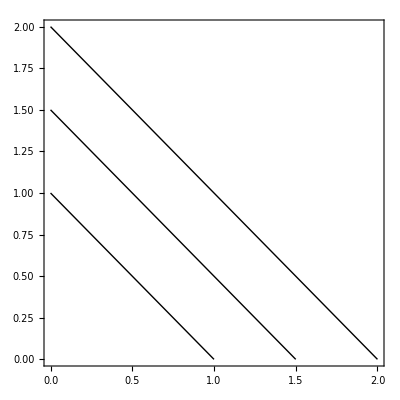

```mathematica
g2=svmDecisionFunctionPlot[df,{x,0,2},{y,0,2},margin->True]
```

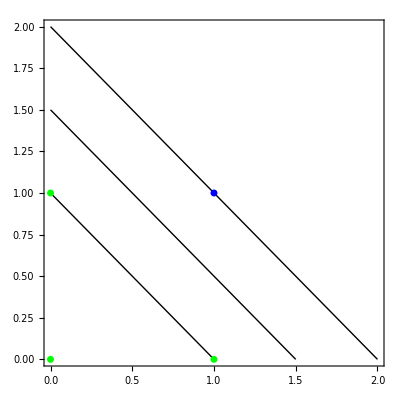

```mathematica
Show[g2,g1]
```

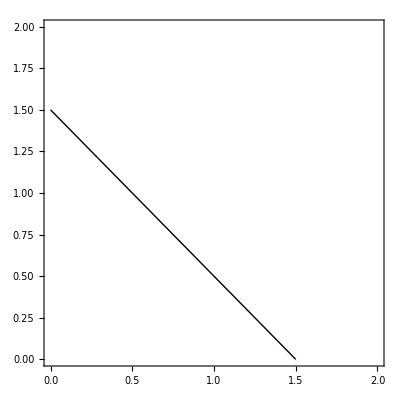

```mathematica
g2=svmDecisionFunctionPlot[df,{x,0,2},{y,0,2}]
```

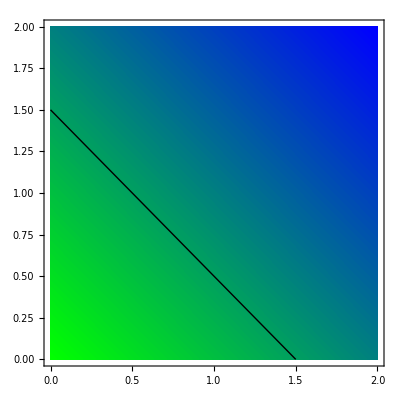

```mathematica
g2=svmDecisionFunctionPlot[df,{x,0,2},{y,0,2},shading->True]
```

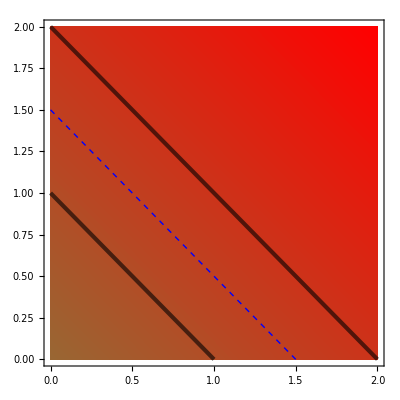

```mathematica
g2=svmDecisionFunctionPlot[df,{x,0,2},{y,0,2},shading->True,shadingColors->{Brown,Red},frontierStyle->{AbsoluteDashing[{4}],Blue},margin->True,marginStyle->{{AbsoluteThickness[3],Opacity[.6]}}]
```

```mathematica
prns={{0,0,0},{0,1,1},{1,0,1},{1,1,0},{0,0,1}};
lbs={1,1,1,-1,-1};
```

```mathematica
df=svmClassification[prns,lbs,kernel->{"gaussian",.3}]
```

{0.803741,0.803741,0.803741,1.20097,1.21025}

Function[{svMathematica`Private`q$},0.200932+0.803741 ⅇ^(-5.55556 Norm[svMathematica`Private`q$-{0,0,0}]^2)-1.21025 ⅇ^(-5.55556 Norm[svMathematica`Private`q$-{0,0,1}]^2)+0.803741 ⅇ^(-5.55556 Norm[svMathematica`Private`q$-{0,1,1}]^2)+0.803741 ⅇ^(-5.55556 Norm[svMathematica`Private`q$-{1,0,1}]^2)-1.20097 ⅇ^(-5.55556 Norm[svMathematica`Private`q$-{1,1,0}]^2)]

```mathematica
g1=svmClassificationSamplePlot[prns,lbs,Axes->True]
```

-Graphics3D-

```mathematica
g2=svmDecisionFunctionPlot[df,{x,0,2},{y,0,2},{z,0,2},margin->True]
```

-Graphics3D-

```mathematica
Show[g2,g1]
```

-Graphics3D-

```mathematica
prns={{0},{0.8},{1}};
lbs={1,-1,-1};
```

```mathematica
df=svmClassification[prns,lbs]
```

{3.125,3.125,9.6×10^-9}

Function[{svMathematica`Private`q$},1.+3.125 {0}.svMathematica`Private`q$-3.125 {0.8}.svMathematica`Private`q$]

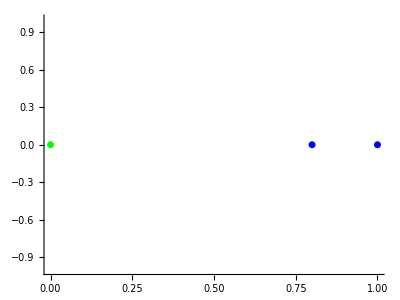

```mathematica
g1=svmClassificationSamplePlot[prns,lbs,Axes->True]
```

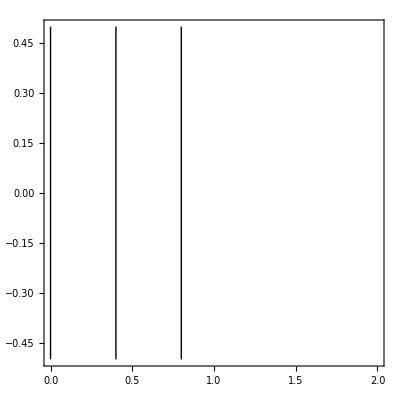

```mathematica
g2=svmDecisionFunctionPlot[df,{x,0,2},margin->True]
```

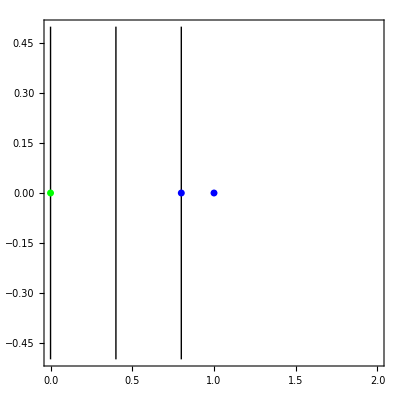

```mathematica
Show[g2,g1]
```

```mathematica
m=30;
prns=Table[{Random[]},{m}];
lbs=Table[Random[],{m}];
```

```mathematica
rf=svmRegression[prns,lbs,implementation->svmLinearInsensitiveRegression,kernel->{"gaussian",.3},c->1000];
```

```mathematica
g1=Plot[rf[{x}],{x,0,1}];
```

```mathematica
g2=svmRegressionSamplePlot[prns,lbs,Frame->True];
```

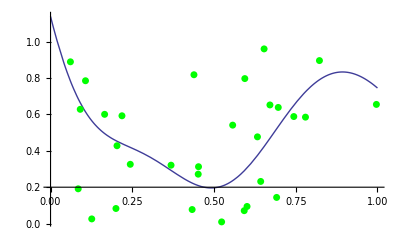

```mathematica
Show[g1,g2,PlotRange->All]
```